# Create New Quantum Gates

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to create new quantum gates.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package.

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## A New Quantum Gate of One Qubit without Explicit Dirac Expression

Use the command SetQuantumGate to specify that a name (ga in this example) is to be consider a Quantum Gate. The first argument is the name of the new quantum gate, and the second argument is the number of input/output qubits of this new gate:

```mathematica
SetQuantumGate[ga,1]
```

The expression ga is a quantum gate of 1 arguments (qubits)

Press the keys [ESC]qg[ESC] in order to obtain the quantum gate template □_OverHat[□], press the [TAB] key  to move between the empty place holders □ and write the gate name (ga in this example, it is the name that was previously defined as a quantum gate) and also write the qubit number or label (3 in this example):

```mathematica
Subscript[ga, OverHat[3]]
```

ga_OverHat[3]

The new quantum gate that was defined above (with the command SetQuantumGate) can be included in the plot of quantum circuits:

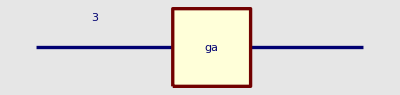

```mathematica
QuantumPlot[Subscript[ga, OverHat[3]]]
```

The new quantum gate cannot be used with more neither less qubits than the number that was specified in SetQuantumGate, therefore next command gives an error because ga cannot be used as a two-qubits gate, and the calculation is aborted:

```mathematica
Subscript[ga, OverHat[3],OverHat[4]]
```

SetQuantumGate::nqb: Quantum gate ga was called with 2 argument(s):{3 ^, 4 ^}. It must have a number na of arguments such that 1<=na<=1

$Aborted

On the other hand, the notation ga_{OverHat[q1],OverHat[q2]}, with curly brackets in the subscript, is used for two gates of one qubit each. Therefore next input is accepted without errors. Press [ESC]qgg[ESC] for the "two gates of one qubit" template □_{OverHat[□],OverHat[□]}

```mathematica
Subscript[ga, {OverHat[3],OverHat[4]}]
```

ga_{OverHat[3],OverHat[4]}

We can use the  two gates of one qubit in a quantum circuit:

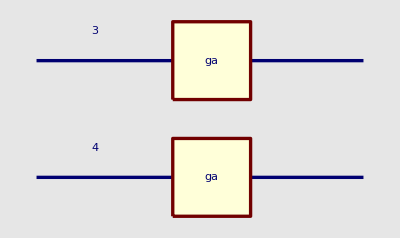

```mathematica
QuantumPlot[Subscript[ga, {OverHat[3],OverHat[4]}]]
```

QuantumEvaluate transforms the notation ga_{OverHat[3],OverHat[4]} into the notation ga_OverHat[3]·ga_OverHat[4]. Both mean the same:  two gates of one qubit:

```mathematica
QuantumEvaluate[Subscript[ga, {OverHat[3],OverHat[4]}]]
```

ga_OverHat[3]·ga_OverHat[4]

Use the [ESC]qn[ESC] template □_□ in order to easily write a large numbre of gates:

```mathematica
Subscript[ga, 5]
```

ga_{OverHat[1],OverHat[2],OverHat[3],OverHat[4],OverHat[5]}

Notice that is very different the interpretation of ga_OverHat[5] from ga_5 (it is very different [ESC]qg[ESC] from [ESC]qn[ESC])

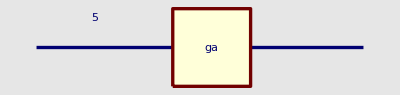
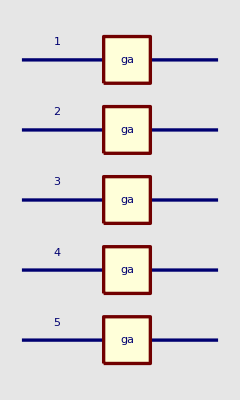

```mathematica
{QuantumPlot[Subscript[ga, OverHat[5]]],QuantumPlot[Subscript[ga, 5]]}
```

This is a "controlled" version of the new gate. Press [ESC]cgate[ESC] for the 𝒞^{OverHat[□]}[□] template.

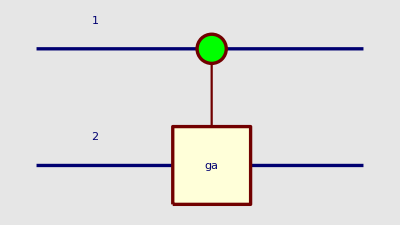

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[ga, OverHat[2]]]]
```

This is the matrix representation of the "controlled" version of the new gate. Press [ESC]cgate[ESC] for the 𝒞^{OverHat[□]}[□] template:

```mathematica
QuantumMatrixForm[(𝒞^{OverHat[1]})[Subscript[ga, OverHat[2]]]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⟨0_OverHat[2]|·ga_OverHat[2]·|0_OverHat[2]⟩ | ⟨0_OverHat[2]|·ga_OverHat[2]·|1_OverHat[2]⟩
0 | 0 | ⟨1_OverHat[2]|·ga_OverHat[2]·|0_OverHat[2]⟩ | ⟨1_OverHat[2]|·ga_OverHat[2]·|1_OverHat[2]⟩)

This is the truth table of the "controlled" version of the new gate. Press [ESC]cgate[ESC] for the 𝒞^{OverHat[□]}[□] template:

```mathematica
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[ga, OverHat[2]]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],0_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | |0_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | |1_OverHat[1]⟩·ga_OverHat[2]·|0_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1]⟩·ga_OverHat[2]·|1_OverHat[2]⟩

Notice that in the following circuit the three gates ga are not in the same column:

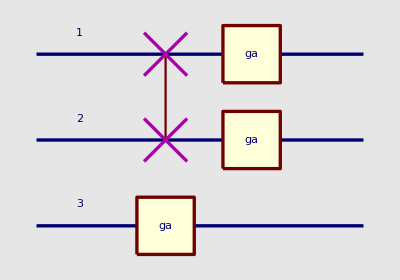

```mathematica
QuantumPlot[(⊗_(j=1)^3 Subscript[ga, ĵ])·Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]
```

Notice that in the following circuit the three gates ga are not in the same column:

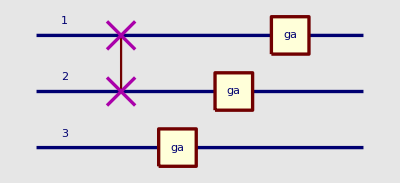

```mathematica
QuantumPlot[(⊗_(j=1)^3 Subscript[ga, ĵ])·Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]],QuantumGateShifting->False]
```

We can plot the three gates in the same column using the □_{OverHat[□],OverHat[□],OverHat[□]} template, which can be entered by pressing the keys [ESC]qggg[ESC] (one q because they are one-qubit gates, three g because there are three gates):

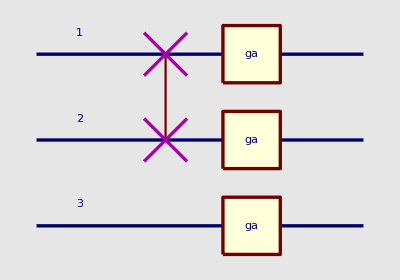

```mathematica
QuantumPlot[Subscript[ga, {OverHat[1],OverHat[2],OverHat[3]}]·Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]
```

QuantumEvaluate transforms ga_{OverHat[1],OverHat[2],OverHat[3]} into ga_OverHat[1]·ga_OverHat[2]·ga_OverHat[3]. Both expressions have the same meaning, but the first one makes QuantumPlot use the same column for the three gates, as was shown above.

```mathematica
QuantumEvaluate[Subscript[ga, {OverHat[1],OverHat[2],OverHat[3]}]]
```

ga_OverHat[1]·ga_OverHat[2]·ga_OverHat[3]

The "quantum register" notation [ESC]qn[ESC] gives more flexibility in the naming of the qubits:

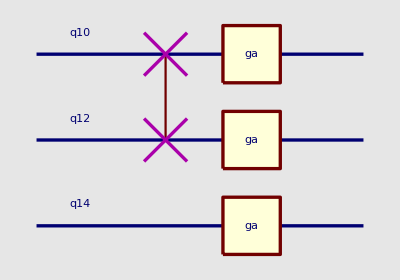

```mathematica
QuantumPlot[Subscript[ga, ℛℯℊ𝒾𝓈𝓉ℯ𝓇[10,14,2,"q"]]·Subscript[𝒮𝒲𝒜𝒫, ℛℯℊ𝒾𝓈𝓉ℯ𝓇[10,12,2,"q"]]]
```

The notation ⊗_(j=1)^3 ga_(ĵ) is transformed to ga_OverHat[1]·ga_OverHat[2]·ga_OverHat[3] without having to use QuantumEvaluate:

```mathematica
⊗_(j=1)^3 Subscript[ga, ĵ]
```

ga_OverHat[1]·ga_OverHat[2]·ga_OverHat[3]

Remember that [ESC]qn[ESC] is very different from [ESC]qg[ESC]

```mathematica
{Subscript[ga, 5],Subscript[ga, OverHat[5]]}
```

{ga_{OverHat[1],OverHat[2],OverHat[3],OverHat[4],OverHat[5]},ga_OverHat[5]}

## A New Quantum Gate of One Qubit with Explicit Dirac Expression

The third (optional) argument of SetQuantumGate is the function that will be applied to the qubit(s) when the gate is inside the QuantumEvaluate command:

```mathematica
SetQuantumGate[gb,1,
Function[{x},1/2 √3 |Subscript[0, x̂]⟩·⟨Subscript[0, x̂]|+1/2 |Subscript[1, x̂]⟩·⟨Subscript[0, x̂]|-1/2 |Subscript[0, x̂]⟩·⟨Subscript[1, x̂]|+1/2 √3 |Subscript[1, x̂]⟩·⟨Subscript[1, x̂]|] ]
```

The expression gb is a quantum gate of 1 arguments (qubits)

The commands above defined gb as a quantum gate with a specific Dirac expression. Here we can see the gate applied to the qubit OverHat[5]

```mathematica
QuantumEvaluate[Subscript[gb, OverHat[5]]]
```

1/2 √3 |0_OverHat[5]⟩·⟨0_OverHat[5]|+1/2 |1_OverHat[5]⟩·⟨0_OverHat[5]|-1/2 |0_OverHat[5]⟩·⟨1_OverHat[5]|+1/2 √3 |1_OverHat[5]⟩·⟨1_OverHat[5]|

Here we can see the gate applied to the qubit m̂

```mathematica
QuantumEvaluate[Subscript[gb, m̂]]
```

1/2 √3 |0_(m̂)⟩·⟨0_(m̂)|+1/2 |1_(m̂)⟩·⟨0_(m̂)|-1/2 |0_(m̂)⟩·⟨1_(m̂)|+1/2 √3 |1_(m̂)⟩·⟨1_(m̂)|

If the gate is not inside QuantumEvaluate, then it will not be transformed to its Dirac expression:

```mathematica
Subscript[gb, OverHat[5]]
```

gb_OverHat[5]

The new quantum gate that was defined above can be included in the plot of quantum circuits:

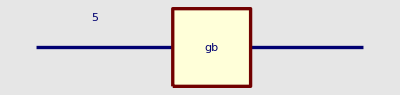

```mathematica
QuantumPlot[Subscript[gb, OverHat[5]]]
```

This is the truth table of the new quantum gate that was defined above:

```mathematica
QuantumTableForm[Subscript[gb, OverHat[5]]]
```

|   Input |   Output
0 | |0_OverHat[5]⟩ | 1/2 √3 |0_OverHat[5]⟩+1/2 |1_OverHat[5]⟩
1 | |1_OverHat[5]⟩ | -1/2 |0_OverHat[5]⟩+1/2 √3 |1_OverHat[5]⟩

This is the matrix representation of the new quantum gate that was defined above:

```mathematica
QuantumMatrixForm[Subscript[gb, OverHat[5]]]
```

((√3)/2 | -1/2
1/2 | (√3)/2)

This is the new gate in terms of Pauli operators:

```mathematica
PauliExpand[Subscript[gb, OverHat[5]]]
```

1/2 √3 σ_(0,OverHat[5])-1/2 ⅈ σ_(𝒴,OverHat[5])

## A New Quantum Gate of Two Qubits With Explicit Dirac Expression

The third (optional) argument of SetQuantumGate is the function that will be applied to the qubit(s) when the gate is inside the QuantumEvaluate command. The second argument (the number 2) indicates that this quantum gate takes as input two qubits, therefore the third argument must be a function of two qubits:

```mathematica
SetQuantumGate[gc,2,
Function[{q1,q2},|Subscript[0, OverHat[q1]],Subscript[0, OverHat[q2]]⟩·⟨Subscript[0, OverHat[q1]],Subscript[0, OverHat[q2]]|-|Subscript[0, OverHat[q1]],Subscript[1, OverHat[q2]]⟩·⟨Subscript[0, OverHat[q1]],Subscript[1, OverHat[q2]]|+|Subscript[1, OverHat[q1]],Subscript[1, OverHat[q2]]⟩·⟨Subscript[1, OverHat[q1]],Subscript[0, OverHat[q2]]|-|Subscript[1, OverHat[q1]],Subscript[0, OverHat[q2]]⟩·⟨Subscript[1, OverHat[q1]],Subscript[1, OverHat[q2]]|] ]
```

The expression gc is a quantum gate of 2 arguments (qubits)

The new quantum gate cannot be used with more neither less qubits than the number that was specified in SetQuantumGate, therefore next command gives an error because gc cannot be used as a one-qubit gate, and the calculation is aborted:

```mathematica
Subscript[gc, OverHat[9]]
```

SetQuantumGate::nqb: Quantum gate gc was called with 1 argument(s):{9 ^}. It must have a number na of arguments such that 2<=na<=2

$Aborted

The new quantum gate gc was defined as a two-qubit gate. Press [ESC]qqg[ESC] for the two-qubits-one-gate template:

```mathematica
Subscript[gc, OverHat[5],OverHat[9]]
```

gc_(OverHat[5],OverHat[9])

The commands above (at the top of this section) defined gc as a quantum gate with a specific Dirac expression. Here we can see the gate applied to the qubits OverHat[5], OverHat[9]

```mathematica
QuantumEvaluate[Subscript[gc, OverHat[5],OverHat[9]]]
```

|0_OverHat[5],0_OverHat[9]⟩·⟨0_OverHat[5],0_OverHat[9]|-|0_OverHat[5],1_OverHat[9]⟩·⟨0_OverHat[5],1_OverHat[9]|+|1_OverHat[5],1_OverHat[9]⟩·⟨1_OverHat[5],0_OverHat[9]|-|1_OverHat[5],0_OverHat[9]⟩·⟨1_OverHat[5],1_OverHat[9]|

This is the truth table of the new quantum gate that was defined above:

```mathematica
QuantumTableForm[Subscript[gc, OverHat[5],OverHat[9]]]
```

|   Input |   Output
0 | |0_OverHat[5],0_OverHat[9]⟩ | |0_OverHat[5],0_OverHat[9]⟩
1 | |0_OverHat[5],1_OverHat[9]⟩ | -|0_OverHat[5],1_OverHat[9]⟩
2 | |1_OverHat[5],0_OverHat[9]⟩ | |1_OverHat[5],1_OverHat[9]⟩
3 | |1_OverHat[5],1_OverHat[9]⟩ | -|1_OverHat[5],0_OverHat[9]⟩

The new quantum gate that was defined above can be included in the plot of quantum circuits:

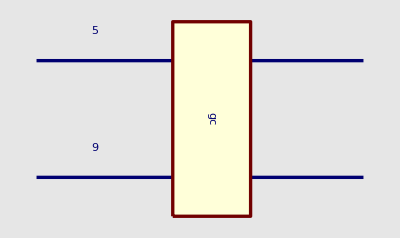

```mathematica
QuantumPlot[Subscript[gc, OverHat[5],OverHat[9]]]
```

The gate is separated in two blocks with the default qubit order. A vertical line is used to indicate that the two bocks represent a single two-qubits gate

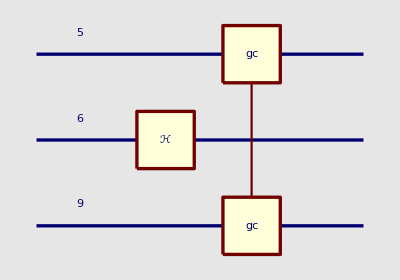

```mathematica
QuantumPlot[Subscript[gc, OverHat[5],OverHat[9]]·Subscript[ℋ, OverHat[6]]]
```

The option QubitList can be used to specify another order for the qubits, so that the gate gc can be plotted as a single block:

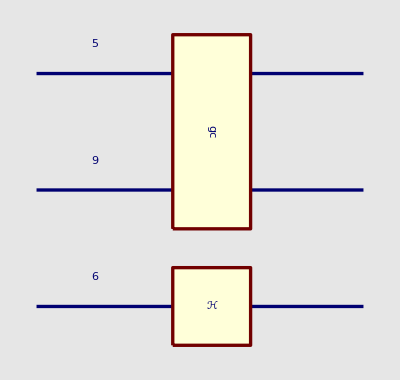

```mathematica
QuantumPlot[Subscript[gc, OverHat[5],OverHat[9]]·Subscript[ℋ, OverHat[6]],QubitList->{OverHat[5],OverHat[9],OverHat[6]}]
```

## A New Quantum Gate With a Number of Qubits Inside a Range

The second argument of SetQuantumGate can be a list of two integers, specifying that the number of qubits for this gate must be within the interval spanned by those integers. If such kind gate is defined with the third (optional) argument of SetQuantumGate, then it is expected that the third argument will be a Function using the standard Mathematica notation for an arbotrary sequence of arguments: ## (SlotSequence).

```mathematica
SetQuantumGate[ge,{2,4},Function[Subscript[ℋ, {##}]·Subscript[𝒳, {##}]]]
```

The expression ge is a quantum gate with a number na of arguments (qubits) such that 2≤na≤4

The quantum gate ge that was defined above cannot be used with only one qubit, therefore we obtain an error message and the calculation is aborted if we try to use it with only one qubit:

```mathematica
Subscript[ge, OverHat[1]]
```

SetQuantumGate::nqb: Quantum gate ge was called with 1 argument(s):{1 ^}. It must have a number na of arguments such that 2<=na<=4

$Aborted

The quantum gate ge can be used with 2, 3 or 4 qubits. Press [ESC]qqg[ESC] for the □_(OverHat[□],OverHat[□]) template:

```mathematica
Subscript[ge, OverHat[1],OverHat[2]]
```

ge_(OverHat[1],OverHat[2])

In order to write the quantum gate with four qubits, first write with three [ESC]qqqg[ESC] □_(OverHat[□],OverHat[□],OverHat[□]), then place the cursor to the right of the last qubit, and write another qubit pressing [ESC]qb[ESC] OverHat[□]

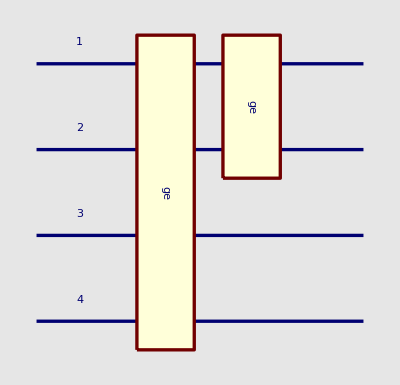

```mathematica
QuantumPlot[Subscript[ge, OverHat[1],OverHat[2]]·Subscript[ge, OverHat[1],OverHat[2],OverHat[3],OverHat[4]]]
```

This is the truth table of ge_(OverHat[1],OverHat[2],OverHat[3]). This command can take several seconds in your computer to evaluate

```mathematica
QuantumTableForm[ Subscript[ge, OverHat[1],OverHat[2],OverHat[3]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

This is the representation of the gate in terms of Pauli operators. This calculation can take several seconds in your computer:

```mathematica
PauliExpand[Subscript[ge, OverHat[1],OverHat[2],OverHat[3]]]
```

(σ_(0,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3]))/(2 √2)+(ⅈ σ_(𝒴,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3]))/(2 √2)+(ⅈ σ_(0,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(0,OverHat[3]))/(2 √2)-(σ_(𝒴,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(0,OverHat[3]))/(2 √2)+(ⅈ σ_(0,OverHat[1])·σ_(0,OverHat[2])·σ_(𝒴,OverHat[3]))/(2 √2)-(σ_(𝒴,OverHat[1])·σ_(0,OverHat[2])·σ_(𝒴,OverHat[3]))/(2 √2)-(σ_(0,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(𝒴,OverHat[3]))/(2 √2)-(ⅈ σ_(𝒴,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(𝒴,OverHat[3]))/(2 √2)

## A New Quantum Gate With a Parameter

Nested Function[] commands can be used in order to define a parametric quantum gate, as shown in the example below. The outer Function[] handles the dependence on the qubits, while the inner Function[] handles the dependence on the parameter:

```mathematica
SetQuantumGate[rot,1,
Function[{q1},
Function[{θ},
Cos[θ]|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|-Sin[θ]|Subscript[0, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]|+Sin[θ]|Subscript[1, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+Cos[θ]|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ]
```

The expression rot is a quantum gate of 1 arguments (qubits)

The "parametric quantum gate" template □_OverHat[□][□] can be entered by pressing the keys [ESC]pqg[ESC].  This is the truth table of the parametric quantum gate that was defined above, when the parameter is π/6 and it is applied to the qubit with label OverHat[3]:

```mathematica
QuantumTableForm[Subscript[rot, OverHat[3]][π/6]]
```

|   Input |   Output
0 | |0_OverHat[3]⟩ | 1/2 √3 |0_OverHat[3]⟩+1/2 |1_OverHat[3]⟩
1 | |1_OverHat[3]⟩ | -1/2 |0_OverHat[3]⟩+1/2 √3 |1_OverHat[3]⟩

The "parametric quantum gate" template □_OverHat[□][□] can be entered by pressing the keys [ESC]pqg[ESC].  This is the truth table of the parametric quantum gate that was defined above, when the parameter is π/12 and it is applied to the qubit with label OverHat[3]:

```mathematica
QuantumTableForm[Subscript[rot, OverHat[3]][π/12]]
```

|   Input |   Output
0 | |0_OverHat[3]⟩ | ((√(3/2))/2+1/(2 √2)) |0_OverHat[3]⟩+((√(3/2))/2-1/(2 √2)) |1_OverHat[3]⟩
1 | |1_OverHat[3]⟩ | (-(√(3/2))/2+1/(2 √2)) |0_OverHat[3]⟩+((√(3/2))/2+1/(2 √2)) |1_OverHat[3]⟩

The "parametric quantum gate" template □_OverHat[□][□] can be entered by pressing the keys [ESC]pqg[ESC].  This is the truth table of the parametric quantum gate that was defined above, when the parameter is π/4 and it is applied to the qubit with label OverHat[3]:

```mathematica
QuantumTableForm[Subscript[rot, OverHat[3]][π/4]]
```

|   Input |   Output
0 | |0_OverHat[3]⟩ | (|0_OverHat[3]⟩)/(√2)+(|1_OverHat[3]⟩)/(√2)
1 | |1_OverHat[3]⟩ | -(|0_OverHat[3]⟩)/(√2)+(|1_OverHat[3]⟩)/(√2)

The parametric quantum gate that was defined above can be included in quantum circuits:

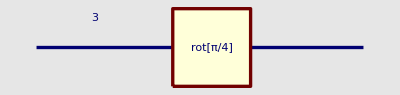

```mathematica
QuantumPlot[Subscript[rot, OverHat[3]][π/4]]
```

This is a "controlled version" of the new parametric quantum gate. Press [ESC]cgate[ESC] for the 𝒞^{OverHat[□]}[□] template, and [ESC]pqg[ESC] for the □_OverHat[□][□] template:

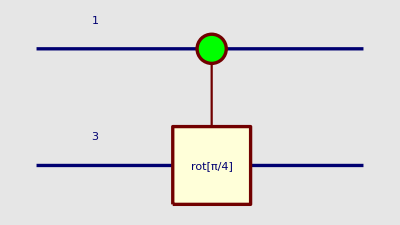

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[rot, OverHat[3]][π/4]]]
```

This is the truth table for a "controlled version" of the new parametric quantum gate. Press [ESC]cgate[ESC] for the 𝒞^{OverHat[□]}[□] template, and [ESC]pqg[ESC] for the □_OverHat[□][□] template:

```mathematica
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[rot, OverHat[3]][π/4]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[3]⟩
1 | |0_OverHat[1],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[3]⟩
2 | |1_OverHat[1],0_OverHat[3]⟩ | (|1_OverHat[1],0_OverHat[3]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3]⟩)/(√2)
3 | |1_OverHat[1],1_OverHat[3]⟩ | -(|1_OverHat[1],0_OverHat[3]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3]⟩)/(√2)

This is a "tensor power" of the parametric quantum gate. Notice that each gate in the answer is applied to a different qubit. Press [ESC]tpow[ESC] for the (□)^(⊗□) template, and [ESC]pqg[ESC] for the □_OverHat[□][□] template:

```mathematica
(Subscript[rot, OverHat[1]][π/4])^(⊗3)
```

rot_OverHat[1][π/4]·rot_OverHat[2][π/4]·rot_OverHat[3][π/4]

This is the truth table of a "tensor power" of the parametric quantum gate. Notice that there are three different qubits in the answer. Press [ESC]tpow[ESC] for the (□)^(⊗□) template, and [ESC]pqg[ESC] for the □_OverHat[□][□] template:

```mathematica
QuantumTableForm[(Subscript[rot, OverHat[1]][π/4])^(⊗3)]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | -(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | -(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | -(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | -(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

Compare the following truth table with the previous one.
The difference is that below we have a "normal power" [ESC]po[ESC]; it means the repeated application of the gate to the same qubit:

```mathematica
QuantumTableForm[(Subscript[rot, OverHat[1]][π/4])^3]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | -(|0_OverHat[1]⟩)/(√2)+(|1_OverHat[1]⟩)/(√2)
1 | |1_OverHat[1]⟩ | -(|0_OverHat[1]⟩)/(√2)-(|1_OverHat[1]⟩)/(√2)

This is a tensor product of an expression that includes the new parametric gate. Press [ESC]tprod[ESC] for the ⊗_(□=□)^□□ template, [ESC]pqg[ESC] for the □_OverHat[□][□] template, [ESC]hg[ESC] for the ℋ_OverHat[□] template and [ESC]on[ESC] for the centerdot · symbol:

```mathematica
⊗_(j=1)^3(Subscript[rot, OverHat[j+1]][π/4]·Subscript[ℋ, ĵ])
```

rot_OverHat[2][π/4]·ℋ_OverHat[1]·rot_OverHat[3][π/4]·ℋ_OverHat[2]·rot_OverHat[4][π/4]·ℋ_OverHat[3]

This is the quantum circuit for the expression. Notice that the three parametric gates are not in the same column:

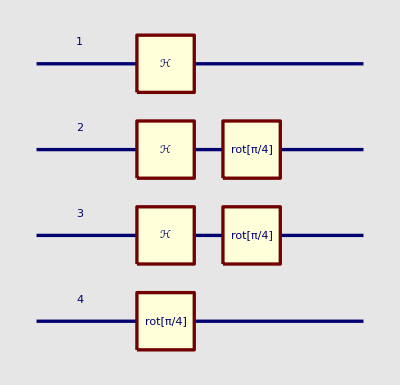

```mathematica
QuantumPlot[⊗_(j=1)^3(Subscript[rot, OverHat[j+1]][π/4]·Subscript[ℋ, ĵ])]
```

The circuit looks more symetrical with the option QuantumGateShifting → False, however the three parametric gates are not in the same column:

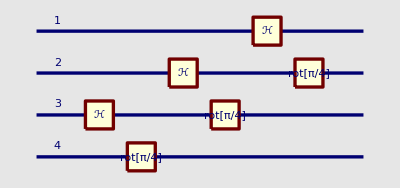

```mathematica
QuantumPlot[⊗_(j=1)^3(Subscript[rot, OverHat[j+1]][π/4]·Subscript[ℋ, ĵ]),QuantumGateShifting->False]
```

Finally a version of the circuit where the three parametric gates are in the same column. Notice that the tensor product template is not used anymore. Instead, press the keys [ESC]pqggg[ESC] for the the □_{OverHat[□],OverHat[□],OverHat[□]}[□] template and [ESC]hggg[ESC] for the ℋ_{OverHat[□],OverHat[□],OverHat[□]} template:

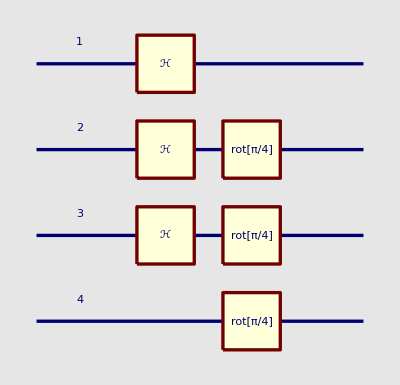

```mathematica
QuantumPlot[Subscript[rot, {OverHat[2],OverHat[3],OverHat[4]}][π/4]·Subscript[ℋ, {OverHat[1],OverHat[2],OverHat[3]}]]
```

These two notations represent the same set of gates, the difference is whether the gates will or will not be plotted in the same column in a quantum circuit:

```mathematica
QuantumEvaluate[Subscript[rot, {OverHat[1],OverHat[2],OverHat[3]}][π/4]]==QuantumEvaluate[⊗_(j=1)^3 Subscript[rot, ĵ][π/4]]
```

True

This is the Dirac expression for our new parametric quantum gate, with parameter π/6:

```mathematica
QuantumEvaluate[Subscript[rot, OverHat[3]][π/6]]
```

1/2 √3 |0_OverHat[3]⟩·⟨0_OverHat[3]|+1/2 |1_OverHat[3]⟩·⟨0_OverHat[3]|-1/2 |0_OverHat[3]⟩·⟨1_OverHat[3]|+1/2 √3 |1_OverHat[3]⟩·⟨1_OverHat[3]|

This is the matrix representation of our new parametric quantum gate, with parameter π/6:

```mathematica
QuantumMatrixForm[Subscript[rot, OverHat[3]][π/6]]
```

((√3)/2 | -1/2
1/2 | (√3)/2)

This is the matrix representation of the hermitian conjugate of our new parametric quantum gate, with parameter π/6. Press [ESC]her[ESC] for the (□)^† template:

```mathematica
QuantumMatrixForm[SuperDagger[(Subscript[rot, OverHat[3]][π/6])]]
```

((√3)/2 | 1/2
-1/2 | (√3)/2)

This is the Pauli expansion of our new parametric quantum gate, with parameter π/6::

```mathematica
PauliExpand[Subscript[rot, OverHat[3]][π/6]]
```

1/2 √3 σ_(0,OverHat[3])-1/2 ⅈ σ_(𝒴,OverHat[3])

If we try yo get the expansion for an arbitrary value of the parameter, in this case t, we get an error, because if t is a complex number, then gate would be nonunitary:

```mathematica
PauliExpand[Subscript[rot, OverHat[3]][t]]
```

PauliExpand::nonunit: PauliExpand can only expand unitary operators
The expression rot_3 ^[t] is or might be nonunitary for some complex values of its parameters.

$Aborted

A simple way to indicate that the parameter is always real is to write Re[t] instead of t. We obtain the correct expansion without any error:

```mathematica
PauliExpand[Subscript[rot, OverHat[3]][Re[t]]]
```

Cos[Re[t]] σ_(0,OverHat[3])-ⅈ Sin[Re[t]] σ_(𝒴,OverHat[3])

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx